```mathematica
Quit
```

```mathematica
LG[Q_]:=Sum[((ⅈ α  L Log[2 n Pi])/(n Pi))^p 1/(p!),{p,0,Q}];
S1[Q_]:=Sum[Pochhammer[1-(α L)/(2 I n Pi),l]Pochhammer[-(α L)/(2 I n Pi),l] 1/(2 I n Pi )^l,{l,0,Q}];
S2[Q_]:=Sum[Pochhammer[1+(α L)/(2 I n Pi),l]Pochhammer[(α L)/(2 I n Pi),l] 1/(-2 I  n Pi )^l,{l,0,Q}];
G1[Q_]:=Normal[Series[1/Gamma[1+α/(2 I λ)],{λ,∞,Q}]]/.{λ->(n Pi)/L};
G2[Q_]:=Normal[Series[1/Gamma[1-α/(2 I λ)],{λ,∞,Q}]]/.{λ-> (n Pi)/L};
Ex[Q_]:=Sum[(2 I ϵ L)^l/(l!),{l,0,Q}];
```

```mathematica
Do[{
	serie =LG[j]S2[j]G2[j]-Ex[j]S1[j]G1[j],
	polinomio = serie/.{ϵ->α/(2 Pi)Log[2 n Pi]/n+Sum[a[p]/n^p,{p,1,j}]},
	coeficiente= Coefficient[polinomio,n,-j],
	sol = Solve[coeficiente==0,a[j]],
	a[j]=a[j]/.{sol[[1]][[1]]},
	Print[Simplify[a[j]]]},
{j,1,7}]
```

(EulerGamma α)/(2 π)

0

(α (12-6 L α+L^2 α^2 PolyGamma[2,1]))/(48 π^3)

0

-(α (17280-4560 L α+360 L^2 α^2+L^4 α^4 PolyGamma[4,1]))/(3840 π^5)

0

(α (435456000-62536320 L α+4253760 L^2 α^2-115920 L^3 α^3+L^6 α^6 PolyGamma[6,1]))/(645120 π^7)

```mathematica
ϵ=(*β/(2 Pi) Log[2 n Pi]/n+(EulerGamma β)/(2 Pi) 1/n*)+(12 β-6 β^2+β^3 PolyGamma[2,1])/(48 π^3) 1/n^3+(-17280 β+4560 β^2-360 β^3-β^5 PolyGamma[4,1])/(3840 π^5)1/n^5+(435456000 β -62536320 β^2+4253760 β^3-115920 β^4+β^7 PolyGamma[6,1])/(645120 π^7)1/n^7;
```

```mathematica
Sum[(n Pi)^(-2s)(1+ϵ/(n Pi)),{n,1,∞}]
```

```mathematica
1/645120 π^(-8-2 s) β (161280 π^4 Zeta[2 (2+s)]-80640 π^4 β Zeta[2 (2+s)]+13440 π^4 β^2 PolyGamma[2,1] Zeta[2 (2+s)]-2903040 π^2 Zeta[2 (3+s)]+766080 π^2 β Zeta[2 (3+s)]-60480 π^2 β^2 Zeta[2 (3+s)]-168 π^2 β^4 PolyGamma[4,1] Zeta[2 (3+s)]+435456000 Zeta[2 (4+s)]-62536320 β Zeta[2 (4+s)]+4253760 β^2 Zeta[2 (4+s)]-115920 β^3 Zeta[2 (4+s)]+β^6 PolyGamma[6,1] Zeta[2 (4+s)])/.{s->-1/2}
```

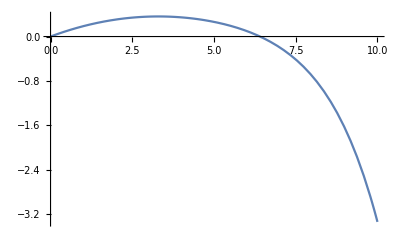

```mathematica
Plot[1/(645120 π^7)β (161280 π^4 Zeta[3]-80640 π^4 β Zeta[3]+13440 π^4 β^2 PolyGamma[2,1] Zeta[3]-2903040 π^2 Zeta[5]+766080 π^2 β Zeta[5]-60480 π^2 β^2 Zeta[5]-168 π^2 β^4 PolyGamma[4,1] Zeta[5]+435456000 Zeta[7]-62536320 β Zeta[7]+4253760 β^2 Zeta[7]-115920 β^3 Zeta[7]+β^6 PolyGamma[6,1] Zeta[7]),{β,0,10}]
```

```mathematica
Expand[1/(645120 π^7)β (161280 π^4 Zeta[3]-80640 π^4 β Zeta[3]+13440 π^4 β^2 PolyGamma[2,1] Zeta[3]-2903040 π^2 Zeta[5]+766080 π^2 β Zeta[5]-60480 π^2 β^2 Zeta[5]-168 π^2 β^4 PolyGamma[4,1] Zeta[5]+435456000 Zeta[7]-62536320 β Zeta[7]+4253760 β^2 Zeta[7]-115920 β^3 Zeta[7]+β^6 PolyGamma[6,1] Zeta[7])]//N
```

0.219798 β-0.0331856 β^2-0.0000580207 β^3-0.0000599901 β^4+0.0000219598 β^5-3.7572×10^-7 β^7